```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<Scrabbology`
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
```

## Version 1: 7 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion1Scrabblegorithm[1]
```

Attempt 1

Bingos Found: {CATCHER}

Tiles Left: 93 AAAAAAAABBDDDDEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRSSSSTTTTTUUUUVVWWXYYZ??

Bingos Found: {CATCHER,HOLLOES}

Tiles Left: 86 AAAAAAAABBDDDDEEEEEEEEEEFFGGGIIIIIIIIIJKLLMMNNNNNNOOOOOOPPQRRRRRSSSTTTTTUUUUVVWWXYYZ??

Bingos Found: {CATCHER,HOLLOES,TIPPEES}

Tiles Left: 79 AAAAAAAABBDDDDEEEEEEEEFFGGGIIIIIIIIJKLLMMNNNNNNOOOOOOQRRRRRSSTTTTUUUUVVWWXYYZ??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS}

Tiles Left: 72 AAAAAAABBDDDDEEEEEEEEFFGGIIIIIIIJKLMMNNNNNOOOOOOQRRRRRTTTTUUUUVVWWXYYZ??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER}

Tiles Left: 65 AAAAAAABBDDDDEEEEEEEFFGGIIIIIIJKLMMNNNNNOOOOQRRRRTTTUUUUVVWWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING}

Tiles Left: 58 AAAAABBDDDDEEEEEEEFFIIIIIKLMMNNNNOOOOQRRRRTTTUUUUVVWWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED}

Tiles Left: 51 AAAAADDDEEEEEEFFIIIIIKMMNNNNOOOQRRRRTTTUUUUVVWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER}

Tiles Left: 44 AAAADDDEEEEEFFIIIIKMMNNNNOOOQRTTTUUUUVWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER,TRITOMA}

Tiles Left: 37 AAADDDEEEEEFFIIIKMNNNNOOQTUUUUVWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER,TRITOMA,EMANATE}

Tiles Left: 30 ADDDEEEFFIIIKNNNOOQUUUUVWXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER,TRITOMA,EMANATE,WAVEOFF}

Tiles Left: 23 DDDEEIIIKNNNOQUUUUXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER,TRITOMA,EMANATE,WAVEOFF,QUININE}

Tiles Left: 16 DDDEIKNOUUUXYY??

Bingos Found: {CATCHER,HOLLOES,TIPPEES,SIGNALS,ZOOTIER,JAGAING,WOBBLED,ARRIVER,TRITOMA,EMANATE,WAVEOFF,QUININE,BUDDIED}

Tiles Left: 9 KNOUUXYY?

No Valid Words

```mathematica
dataV1=CloudGet["V.1-WordMaster"];
```

```mathematica
Dataset[dataV1]
```

### Visualize

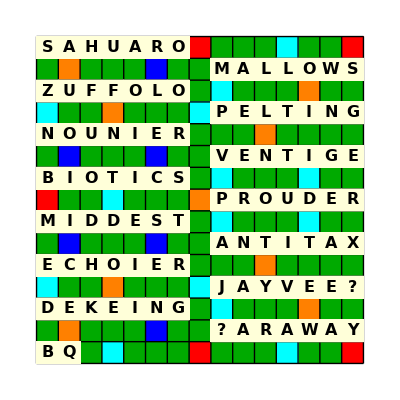

```mathematica
VisualizeVersion1[dataV1[[-1]]]
```

## Version 2: 8 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion2Scrabblegorithm[1]
```

Bingos: {SCOGGED}

Tiles Left: 93 AAAAAAAAABBCDDDEEEEEEEEEEEFFGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOPPQRRRRRRSSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 7 CDEGGOS

SLIPPILY played through: S

Bingos: {SCOGGED,SLIPPILY}

Tiles Left: 86 AAAAAAAAABBCDDDEEEEEEEEEEEFFGHHIIIIIIIJKLLMMNNNNNNOOOOOOOQRRRRRRSSSTTTTTTUUUUVVWWXYZ??

Tiles Used: 14 CDEGGIILLOPPSY

LUSTRATE played through: L

Bingos: {SCOGGED,SLIPPILY,LUSTRATE}

Tiles Left: 79 AAAAAAAABBCDDDEEEEEEEEEEFFGHHIIIIIIIJKLLMMNNNNNNOOOOOOOQRRRRRSSTTTTUUUVVWWXYZ??

Tiles Used: 21 ACDEEGGIILLOPPRSSTTUY

SHIFTIER played through: R

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER}

Tiles Left: 72 AAAAAAAABBCDDDEEEEEEEEEFGHIIIIIJKLLMMNNNNNNOOOOOOOQRRRRRSTTTUUUVVWWXYZ??

Tiles Used: 28 ACDEEEFGGHIIIILLOPPRSSSTTTUY

DITHERED played through: D

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED}

Tiles Left: 65 AAAAAAAABBCDDEEEEEEEFGIIIIJKLLMMNNNNNNOOOOOOOQRRRRSTTUUUVVWWXYZ??

Tiles Used: 35 ACDDEEEEEFGGHHIIIIILLOPPRRSSSTTTTUY

AVIGATOR played through: I

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR}

Tiles Left: 58 AAAAAABBCDDEEEEEEEFIIIIJKLLMMNNNNNNOOOOOOQRRRSTUUUVWWXYZ??

Tiles Used: 42 AAACDDEEEEEFGGGHHIIIIILLOOPPRRRSSSTTTTTUVY

KNARRIER played through: E

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER}

Tiles Left: 51 AAAAABBCDDEEEEEEEFIIIJLLMMNNNNNOOOOOOQSTUUUVWWXYZ??

Tiles Used: 49 AAAACDDEEEEEFGGGHHIIIIIIKLLNOOPPRRRRRRSSSTTTTTUVY

SEMIBOLD played through: S

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD}

Tiles Left: 44 AAAAABCDEEEEEEFIIJLMNNNNNOOOOOQSTUUUVWWXYZ??

Tiles Used: 56 AAAABCDDDEEEEEEFGGGHHIIIIIIIKLLLMNOOOPPRRRRRRSSSTTTTTUVY

UNMANTLE played through: N

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD,UNMANTLE}

Tiles Left: 37 AAAABCDEEEEEFIIJNNNNOOOOOQSUUVWWXYZ??

Tiles Used: 63 AAAAABCDDDEEEEEEEFGGGHHIIIIIIIKLLLLMMNNOOOPPRRRRRRSSSTTTTTTUUVY

EVINCIVE played through: V

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD,UNMANTLE,EVINCIVE}

Tiles Left: 30 AAAABDEEEFJNNNOOOOOQSUUWWXYZ??

Tiles Used: 70 AAAAABCCDDDEEEEEEEEEFGGGHHIIIIIIIIIKLLLLMMNNNOOOPPRRRRRRSSSTTTTTTUUVVY

BEEFWOOD played through: E

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD,UNMANTLE,EVINCIVE,BEEFWOOD}

Tiles Left: 23 AAAAEEJNNNOOOQSUUWXYZ??

Tiles Used: 77 AAAAABBCCDDDDEEEEEEEEEEFFGGGHHIIIIIIIIIKLLLLMMNNNOOOOOPPRRRRRRSSSTTTTTTUUVVWY

ANONYMAS played through: M

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD,UNMANTLE,EVINCIVE,BEEFWOOD,ANONYMAS}

Tiles Left: 16 AAEEJNOOQUUWXZ??

Tiles Used: 84 AAAAAAABBCCDDDDEEEEEEEEEEFFGGGHHIIIIIIIIIKLLLLMMNNNNNOOOOOOPPRRRRRRSSSSTTTTTTUUVVWYY

CABEZONE played through: B with a blank C

Bingos: {SCOGGED,SLIPPILY,LUSTRATE,SHIFTIER,DITHERED,AVIGATOR,KNARRIER,SEMIBOLD,UNMANTLE,EVINCIVE,BEEFWOOD,ANONYMAS,CABEZONE}

Tiles Left: 9 AJOQUUWX?

Tiles Used: 91 AAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIKLLLLMMNNNNNNOOOOOOOPPRRRRRRSSSSTTTTTTUUVVWYYZ?

No Valid Words

```mathematica
dataV2=CloudGet["V.2-WordMaster"];
```

```mathematica
Dataset[dataV2]
```

### Visualize

```mathematica
data=RandomChoice[dataV2]
```

<|Bingos→{TINCHEL,TONETTES,EKISTICS,ANIMATES,WEENIEST,DEVELOPE,HALLOWER,PRANDIAL,OVERNAME,GUARDDOG,BOOBYISH,JANIZARY,FURFUROL,QUADDING},Overlaps→{T,E,I,S,E,H,L,A,D,S,N,R,D},Blanks→{L,N},Tiles Remaining→{I,X}|>

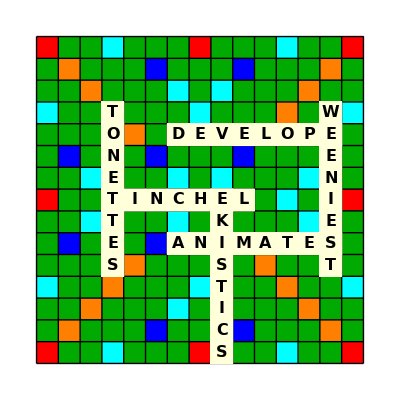

```mathematica
VisualizeVersion2[game_]:=Module[{epilog,board=CreateInitialScrabbleBoard[],bingos=game["Bingos"]},(*Place Bingos on board.*)
epilog=UpdateScrabbleBoard[bingos[[1]],{"H",4},"Right",{}];
epilog=UpdateScrabbleBoard[bingos[[2]],{"D",4},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[3]],{"H",9},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[4]],{"J",7},"Right",epilog];
epilog=UpdateScrabbleBoard[bingos[[5]],{"D",14},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[6]],{"E",7},"Right",epilog];
Show[board,ImageSize->400,Epilog->epilog]
]

VisualizeVersion2[data]
```

## Version 3: Actual Scrabble Game

```mathematica
tiles
```

<|A→<|Quantity→9,Points→1|>,B→<|Quantity→2,Points→3|>,C→<|Quantity→2,Points→3|>,D→<|Quantity→4,Points→2|>,E→<|Quantity→12,Points→1|>,F→<|Quantity→2,Points→4|>,G→<|Quantity→3,Points→2|>,H→<|Quantity→2,Points→4|>,I→<|Quantity→9,Points→1|>,J→<|Quantity→1,Points→8|>,K→<|Quantity→1,Points→5|>,L→<|Quantity→4,Points→1|>,M→<|Quantity→2,Points→3|>,N→<|Quantity→6,Points→1|>,O→<|Quantity→8,Points→1|>,P→<|Quantity→2,Points→3|>,Q→<|Quantity→1,Points→10|>,R→<|Quantity→6,Points→1|>,S→<|Quantity→4,Points→1|>,T→<|Quantity→6,Points→1|>,U→<|Quantity→4,Points→1|>,V→<|Quantity→2,Points→4|>,W→<|Quantity→2,Points→4|>,X→<|Quantity→1,Points→8|>,Y→<|Quantity→2,Points→4|>,Z→<|Quantity→1,Points→10|>,?→<|Quantity→2,Points→0|>|>

```mathematica
(* Initialize. *)
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
board=CreateInitialScrabbleBoard[]; (* Create Graphic of Empty Scrabble Board. *)
assoc=<||>;

i=1;
While[Length[assoc] < 14,
(* Turn 1. *)
While[Length[assoc]==0,
remainingCounts=tiles[[All,"Quantity"]]; (* Whole tile bag remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]]; (* Initially zero tiles have been used. *)
b = BlanksAllowed[assoc, usedCounts];
Module[{next=False},
pos={"H",2};
word=wordsByLength[7][[i]];
If[UpdateRemainingTileCount[remainingCounts,word,b]===tiles[[All,"Quantity"]], (* Starting 7-letter word must not require blanks. *)
Print[word, ": Choose another Starter"];
next=True
];

Module[{boardTurn1},
   boardTurn1=
    Row[
{
DynamicModule[
{currentBoard=board,localEpilogState},
localEpilogState=UpdateScrabbleBoard[word,pos, "Right",{}];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->localEpilogState],
	Button[
		"Select",
		AppendTo[assoc,1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>];
		remainingCounts =UpdateRemainingTileCount[remainingCounts,word,b];
		usedCounts=UpdateUsedTileCount[usedCounts,word];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]];
		]
	}]
	],
Button["Skip",next=True;NotebookDelete[EvaluationCell[]]]}
];
If[next==False,Print[boardTurn1]];
WaitUntil[next===True];
next=False;
   ];
];
i++;
If[i>Length[wordsByLength[7]],Abort[]];
If[Length[assoc]==1, i=1]
];

(* Turns 2-12. *)
While[1<=Length[assoc]<12,
Module[{next=False},(* Initialize flag. *)
word=wordsByLength[8][[i]];
overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
If[overlapTileOptions==={},Print[word," Has No Overlaps!"]; next=True];
b=BlanksAllowed[assoc,usedCounts];
Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that can be formed with the available tiles. *)
]&,overlapTileOptions
];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={}, next=True];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
  
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		Print["Bingos Checked: ",i];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; 
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Abort[]];
If[Length[assoc]==12, i=1]
];

(* Turns 13 and 14. *)
Module[{next=False},(* Initialize flag. *)
word=wordsByLength[8][[i]];
overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]; 
 If[overlapTileOptions==={},Print[word," Has No Overlaps!"];next=True];
b=BlanksAllowed[assoc,usedCounts];
blankAssoc={};
  (* Identify blanks and update blankAssoc. *)
  Map[
    Module[{newRemainingCounts,negativeKeys},
	newRemainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b];
	If[newRemainingCounts==remainingCounts,
        overlapTileOptions=DeleteCases[overlapTileOptions,#],
	negativeKeys=Flatten[Table[#,{-newRemainingCounts[#]}]&/@Select[Keys[newRemainingCounts],newRemainingCounts[#]<0&]];
        If[negativeKeys=!={},
         AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->negativeKeys|>],
	AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->Null|>]
        ]
      ]
    ]&,
    overlapTileOptions
  ];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={}, next=True,
Echo@word;
{overlapVectors,possibleEpilogs} =
Module[
{vectors,epilogs,
blankVectors,wordOptions,blankEpilogs},
vectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]==Null&];
epilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,vectors];
blankVectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]=!=Null&];
blankVectors=Map[Append[#,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
wordOptions=AssociationMap[FormatWordWithBlanks[word,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
blankEpilogs=AssociationMap[UpdateScrabbleBoard[StringReplace[wordOptions[#],c_/;LowerCaseQ[c]:>"?"],#[[1]],#[[2]],epilogState]&,blankVectors];
{Join[vectors,blankVectors],Join[epilogs,blankEpilogs]}
];
];
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		i=1;
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		If[Length[overlapVectors[[dIdx]]]==5,
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->Flatten[{overlapVectors[[dIdx]][[3]],overlapVectors[[dIdx]][[5]]}]]]];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],Length[overlapVectors[[dIdx]][[5]]]];
		Map[remainingCounts[#]++&,overlapVectors[[dIdx]][[5]]];
		usedCounts["?"]=usedCounts["?"]+Length[overlapVectors[[dIdx]][[5]]],
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],0]
		];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; 
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Abort[]];
]
```

KIEKIES: Choose another Starter

KABAKAS: Choose another Starter

Tiles Used: 7 AEGIMSS

Tiles Left: 93 AAAAAAAABBCCDDDDEEEEEEEEEEEFFGGHHIIIIIIIIJKLLLLMNNNNNNOOOOOOOOPPQRRRRRRSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 14 AAEGHIIMPSSSWW

Tiles Left: 86 AAAAAAABBCCDDDDEEEEEEEEEEEFFGGHIIIIIIIJKLLLLMNNNNNNOOOOOOOOPQRRRRRRSTTTTTTUUUUVVXYYZ??

Bingos Checked: 1

Tiles Used: 21 AAEEGHIIIMNOOPSSSSWWZ

Tiles Left: 79 AAAAAAABBCCDDDDEEEEEEEEEEFFGGHIIIIIIJKLLLLMNNNNNOOOOOOPQRRRRRRTTTTTTUUUUVVXYY??

Bingos Checked: 14

Tiles Used: 28 AACEEGGHIIIIJLMNOOOPSSSSUWWZ

Tiles Left: 72 AAAAAAABBCDDDDEEEEEEEEEEFFGHIIIIIKLLLMNNNNNOOOOOPQRRRRRRTTTTTTUUUVVXYY??

Bingos Checked: 26

Tiles Used: 35 AAAAACEEGGHHIIIIJLMNNNOOOPSSSSUVWWZ

Tiles Left: 65 AAAABBCDDDDEEEEEEEEEEFFGIIIIIKLLLMNNNOOOOOPQRRRRRRTTTTTTUUUVXYY??

Bingos Checked: 61

Tiles Used: 42 AAAAACCEEEGGGHHIIIIJLLMNNNNOOOOPSSSSUVWWYZ

Tiles Left: 58 AAAABBDDDDEEEEEEEEEFFIIIIIKLLMNNOOOOPQRRRRRRTTTTTTUUUVXY??

Bingos Checked: 79

Tiles Used: 49 AAAAAACCEEEGGGHHIIIIIJLLMNNNNOOOOOOPRRSSSSTUVWWYZ

Tiles Left: 51 AAABBDDDDEEEEEEEEEFFIIIIKLLMNNOOPQRRRRTTTTTUUUVXY??

Bingos Checked: 153

Tiles Used: 56 AAAAAAACCEEEGGGHHIIIIIIIJLLLMNNNNOOOOOOPRRRSSSSTTUVWWYYZ

Tiles Left: 44 AABBDDDDEEEEEEEEEFFIIKLMNNOOPQRRRTTTTUUUVX??

Bingos Checked: 155

Tiles Used: 63 AAAAAAAACCEEEEGGGHHIIIIIIIIJLLLMNNNNOOOOOOPRRRRRSSSSTTTTUVWWYYZ

Tiles Left: 37 ABBDDDDEEEEEEEEFFIKLMNNOOPQRTTUUUVX??

Bingos Checked: 227

Tiles Used: 70 AAAAAAAAACCDEEEEEGGGHHIIIIIIIIIJLLLMNNNNOOOOOOPRRRRRRSSSSTTTTTTUVWWYYZ

Tiles Left: 30 BBDDDEEEEEEEFFKLMNNOOPQUUUVX??

Bingos Checked: 249

Tiles Used: 77 AAAAAAAAABCCDDEEEEEEGGGHHIIIIIIIIIJKLLLMNNNNNNOOOOOOPRRRRRRSSSSTTTTTTUUVWWYYZ

Tiles Left: 23 BDDEEEEEEFFLMOOPQUUVX??

Bingos Checked: 772

Tiles Used: 84 AAAAAAAAABBCCDDDEEEEEEEEFFGGGHHIIIIIIIIIJKLLLMNNNNNNOOOOOOPRRRRRRSSSSTTTTTTUUUVWWYYZ

Tiles Left: 16 DEEEELMOOPQUVX??

Bingos Checked: 9218

VOLVOXES

Tiles Used: 91 AAAAAAAAABBCCDDDEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMNNNNNNOOOOOOOOPRRRRRRSSSSTTTTTTUUUVVWWXYYZ?

Tiles Left: 9 DEEEMPQU?

25% Bingos Checked

QUEENDOM

Tiles Used: 98 AAAAAAAAABBCCDDDDEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPQRRRRRRSSSSTTTTTTUUUUVVWWXYYZ??

Tiles Left: 2 EP

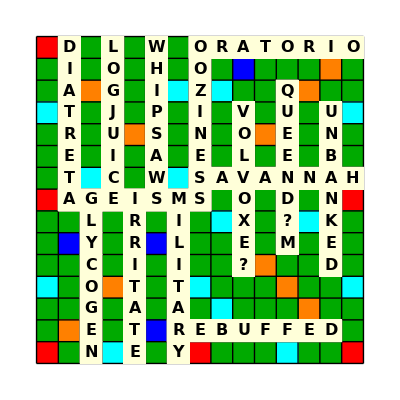

```mathematica
Show[board,Epilog->epilogState]
Dataset[assoc]
```